The Suzuki-Trotter decomposition can be used to approximate the time evolution of a quantum system with a Hamiltonian that can be expressed as the sum of multiple non-commuting terms.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Create a list of operators using a Hamiltonian as 3-qubits interacting based on Ising model H=X_1 X_2+X_2 X_3:

```mathematica
ops={QuantumOperator["X",{1,2}],QuantumOperator["X",{2,3}]};
```

Using QuantumCircuitOperator[{"Trotterization",ops,order,steps,time}], one can create the corresponding quantum circuit for a list of operators (ops), a given order (1,2,4,6,...), number of steps, and time (which is based on Suzuki's recursion relation).

Suzuki-Trotter decomposition of 1st order, one step and time t:

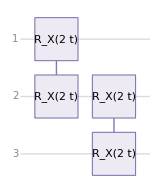

```mathematica
QuantumCircuitOperator[{"Trotterization",ops,1,1,t}]["Diagram"]
```

Suzuki-Trotter decomposition of 2nd order, one step and time t:

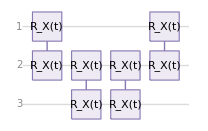

```mathematica
QuantumCircuitOperator[{"Trotterization",ops,2,1,t}]["Diagram"]
```

2nd order, with 4 steps:

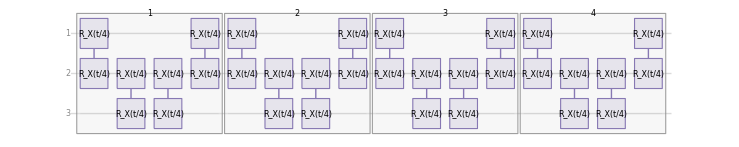

```mathematica
QuantumCircuitOperator[{"Trotterization",ops,2,4,t}]["Diagram",FontSize->8]
```

4th order, only 1 step:

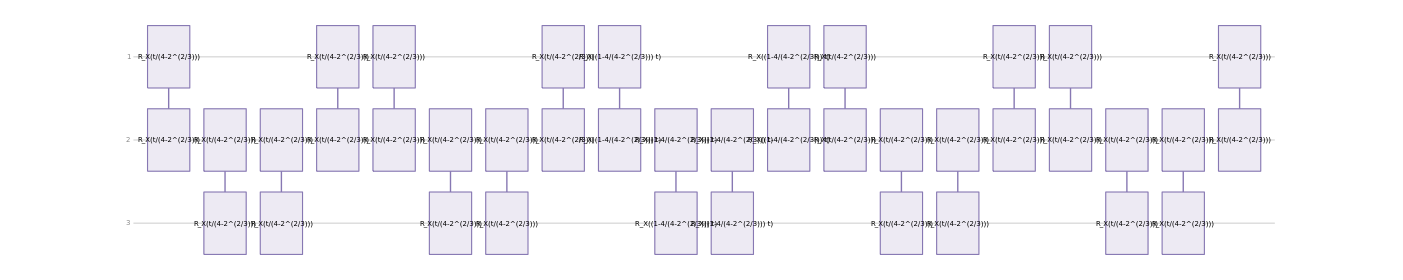

```mathematica
QuantumCircuitOperator[{"Trotterization",ops,4,1,t}]["Diagram",FontSize->7]
```